```mathematica
g[f_, a0_, b0_, tol_]:=Module[{c = (a0+b0)/2, b = N[b0], a = N[a0]},
	 If[f[a]*f[b]>0, Abort[]]; 
	 If[f[a]==0, Return[{a, f[a]} Abort[]; ]];
          If[f[b]==0, Return[{b,f[b]} Abort[];]]; 
	
    While[Abs[b-a]>tol&&Abs[f[c]]>tol,
	If[f[b]*f[c]>0, b=c, a=c];
	c = (a+b)/2;
	];
Return[{c,f[c]}]
   ]
```

```mathematica
g[Function[x,(x^2) - 3],1,3,.01]
```

{1.73438,0.00805664}

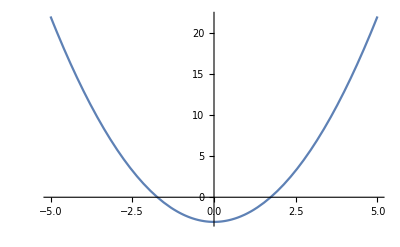

```mathematica
Plot[x^2 - 3, {x, -5,5}]
```